# Analyzing Economic Trends: A Comparative Study of Non-Linear Models,State-Space Models and Neural Networks

Muhammad Ali Hafeez

This computational essay explores the predictive accuracy of three models: non-linear model fits, state space models, and neural nets. The essay takes you on a journey from simple modeling techniques to discover the advantages of these techniques in a world where neural nets are gaining popularity. It is important to note that these modeling techniques are often used in conjunction with each other. However, for the purpose of comparing the models, they will be considered independently.

## Introduction

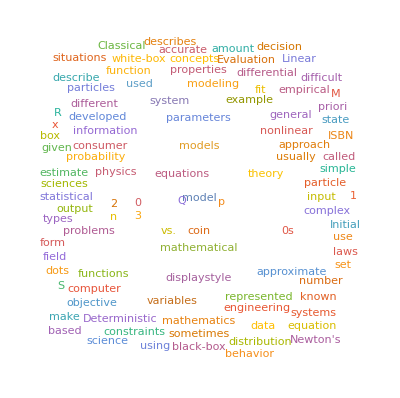

```mathematica
WordCloud[WikipediaData["Mathematical Modeling"]]
```

The purpose of this essay is to introduce a highly significant discussion. The emergence of machine learning has brought about groundbreaking advancements. However, have we thoroughly analyzed each technique in terms of their predictive power relative to one another? This essay aims to compare two crucial techniques: State-Space Models, specifically those employing the Kalman filter, and Neural Networks, which represent a more contemporary approach.

## Data

The data that will be used in this computational essay is the Federal Reserve of Economic Data (FRED) Real Gross Domestic Product data from 1947 to 2023.

```mathematica
data=Import["C:\\Users\\ali12\\Downloads\\GDP.xls"];
preprocessedData=data/. Null->"";
Dataset[preprocessedData]
```

```mathematica
gDPdataIcon=Iconize[preprocessedData,"GDPData"]
```

## Splitting the Data into Train and Test Sets

In this context, we will employ Mathematica to partition the dataset into separate testing and training sets. This division serves the purpose of evaluating the predictive capabilities of our models and safeguarding against the occurrence of overfitting.

```mathematica
whole=preprocessedData;
{trainer,tester}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole,11],Shuffle->False];
Take[Dataset[trainer],10];
Take[Dataset[tester],10];
```

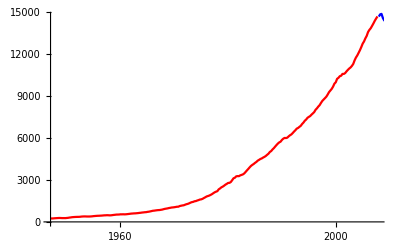

```mathematica
Show[ListLinePlot[TimeSeries[trainer],PlotStyle->Red],ListLinePlot[TimeSeries[tester],PlotStyle->Blue]]
```

## Adjustments to the Data (Relative Time)

```mathematica
InsertedvaluesTrain=Values[trainer];
InsertedvaluesTest=Values[tester];
InsertedkeysTrain=Range[0,0.25*(Length[InsertedvaluesTrain]-1),0.25];
InsertedkeysTest=Range[61,0.25*(Length[InsertedvaluesTest]-1)+61,0.25];
threadedValuesOfTrain=Thread[InsertedkeysTrain->InsertedvaluesTrain];
threadedValuesOfTest=Thread[InsertedkeysTest->InsertedvaluesTest];
Take[Dataset[threadedValuesOfTrain],10]
Take[Dataset[threadedValuesOfTest],10]
```

## Using A Non-Linear Model

NonlinearModelFit::fitd: First argument whole2 in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[whole2,e+a x+b x^2+c x^3+d x^4,{a,b,c,d,e},x]

NonlinearModelFit[whole2,e+a x+b x^2+c x^3+d x^4,{a,b,c,d,e},x]

NonlinearModelFit::fitd: First argument whole2 in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

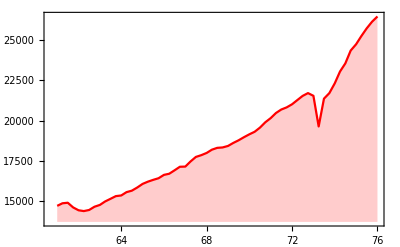
-Graphics-Gross Domestic Product ($)Time since 1947 (years)

```mathematica
Clear[maxX];
Clear[minX];
output=List@@@whole2;
whole3=Testrules;
output2=List@@@whole3;
model=a x+b x^2+c x^3+d x^4+e;
nlm=NonlinearModelFit[output,model,{a,b,c,d,e},x]
equation=Normal[nlm]
xValues=output2[[All,1]];
maxX=Max[xValues];
minX=Min[xValues];
(*Show[ListPlot[output2,PlotStyle->Red],Plot[nlm[x],{x,minX,maxX}],Frame->True,PlotStyle->Blue]*)
plotofmethod=Plot[nlm[x],{x,minX,maxX},Filling->Axis];
plotoftests=ListLinePlot[output2,PlotStyle->Red,Filling->Axis];

Labeled[Show[plotoftests,plotofmethod,Frame->True,PlotStyle->Blue],{"Gross Domestic Product ($)","Time since 1947 (years)"},{Left,Top},RotateLabel->True
]
```

## Using State Space Modeling

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[whole2].

TimeSeriesModelFit::tsmfdt: The data Flatten[whole2] cannot be interpreted as real-valued temporal data.

TimeSeriesModelFit[Flatten[whole2]]

TimeSeriesModelFit[Flatten[whole2]]

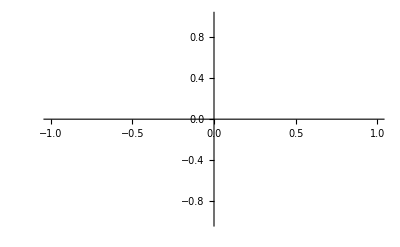
-Graphics-Gross Domestic Product ($)Time

```mathematica
output4=output;
output5=output2;
resultremovedfirstTrain=Map[Rest,output4];
resultremovedfirstTest=Map[Rest,output5];
improvedTrainresult=Flatten[resultremovedfirstTrain];
improvedTestresult=Flatten[resultremovedfirstTest];
tsm=TimeSeriesModelFit[improvedTrainresult]
normaltsm=Normal[tsm]
Labeled[Show[ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{10}]},Filling->Axis],ListPlot[output5,PlotStyle->Red]],{"Gross Domestic Product ($)","Time"},{Left,Top},RotateLabel->True
]
```

## Using Neural Networks

NetChain[<>]

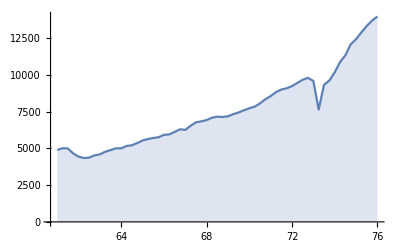
-Graphics-Gross Domestic Product ($)Error between the nueral net and test data

```mathematica
trainingData=Trainrules;
newKeyData=Keys[Testrules];
net=NetChain[{LinearLayer[10],Ramp,LinearLayer[1]}];
trainedNet=NetTrain[net,trainingData,LossFunction->MeanSquaredLossLayer[],Method->"ADAM",MaxTrainingRounds->10000,ValidationSet->Testrules]
testmodel={80,100,110,200};
trainedNet[testmodel];
NetPredictedValues=trainedNet[newKeyData];
graphicalrepnet=Thread[newKeyData->NetPredictedValues];
TestrulesNeccessaryState=Map[List,Testrules];
TestrulesNeccessaryalpha=Flatten[TestrulesNeccessaryState,1];
ErrorPresentedbetween=MapThread[#1[[1]]->(#1[[2]]-#2[[2]])&,{graphicalrepnet,TestrulesNeccessaryalpha}];
NegativeErrorPresentedbetween=Map[#1[[1]]->-#1[[2]]&,ErrorPresentedbetween];
Labeled[ListLinePlot[NegativeErrorPresentedbetween/. Rule->List,Filling->Axis],{"Gross Domestic Product ($)","Error between the nueral net and test data"},{Left,Top},RotateLabel->True
]
```

## Estimated Errors and their Implications

By a manual computation these are the estimated error areas of each model :

Non-linear model fit: The estimated area of the blue region is approximately 140,000 square units.

State Space Model: The estimated area between the red line and the blue line is approximately 2,300,000 square units.

Neural Net: The estimated area between the blue line and the x-axis is approximately 112,000 square units.

Based on the above results, we could conclude that on a limited amount of data a neural net would be the most appropriate simple model to use to make predictions on limited data.

## Limitations

Some limitations of the results include:

The existence of a limited amount of data may give rise to a circumstance wherein one method appears comparatively more appropriate than another.

The complexity of each algorithm may make one model better than the other and the complexity was not used as a quality indicator here.

Each model necessitated varying degrees of data cleaning; for instance, manipulating date objects in state space modeling was simpler, and the utilization of relative time was unnecessary.

It is worth noting that the simplicity of each model constituted a limitation to their predictive power.